```mathematica
(* Coronavirus: *)
transmissionRate=2
```

2

```mathematica
(* Estimate of Current Number of Cases in Madrid (14/03/2020) *)
currentNumberOfCases=Mean[{10000,60000}]
```

35000

```mathematica
(* Compute transmition rate, assuming it doubles every two days and a half: *)
y[d_]=.
RSolve[{y[d+5/2]==2y[d], y[0]==35000}, y[d], d]/.{C[1]-> 1,C[2]-> 0}//Flatten
```

{y[d]→4375 2^(3+(2 d)/5)}

```mathematica
(* Use it: *)
y[d_]:= 4375 transmissionRate^(3+2/5d)
```

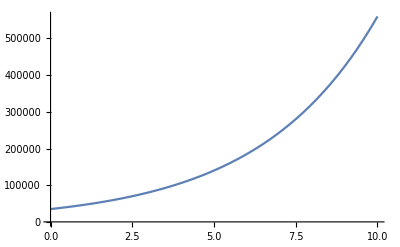

```mathematica
Plot[y[d],{d, 0, 10}]
```

```mathematica
(* Madrid city data (outdated) *)
madridPopulation = CityData[{"Madrid", "Madrid", "Spain"}, "Population"]//QuantityMagnitude
```

3273049

```mathematica
Solve[y[d]==madridPopulation, d]/.C[1]-> 0//N//Flatten
```

{d→16.3678}

```mathematica
madridPopulation=6550000
```

6550000

```mathematica
Solve[y[d]==madridPopulation, d]/.C[1]-> 0//N//Flatten
```

{d→18.87}

```mathematica
(* Spain data *)
spainPopulation = CountryData["Spain", "Population"]//QuantityMagnitude
```

46354321

```mathematica
(* "Real" infection rate (counting asymptomatics) *)
infectionRate=1/3
```

1/3

```mathematica
(* Number of deaths (19/04/20) (twice) *)
deaths = 2 20639
```

41278

```mathematica
(* Real deatch rate: *)
deathRate = deaths / spainPopulation / infectionRate;
deathRate //N
```

0.00267147

```mathematica
(* Real number of deaths: *)
spainPopulation deathRate
```

123834